Exact formulas for the asymmetric vortex sheet solution:

Δ==exp ı γ λ R_0

B==-q-2 exp ı p λ

```mathematica
PlotBoundary[R0_,λ_] :=
ParametricPlot[With[{η=R0 /Cos[λ-θ] Exp[I θ] },{Re[η],Im[η]}],{θ,-Pi,Pi}];
```

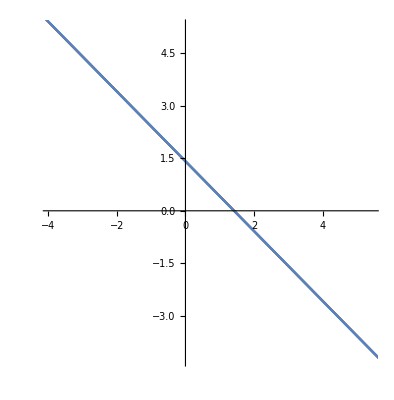

```mathematica
PlotBoundary[1,Pi/4]
```

```mathematica
Test[R0_,p_,q_, λ_,γ_,θ_] :=
Module[{},
Σ = R0 Exp[I(λ-θ)];
Δ = γ R0 Exp[-I λ];
B = -q - p Exp[2I λ];
η=Im[Σ] Exp[I θ];
SubPlus[V] =  Δ/2 +B η;
SubMinus[V] =-Δ/2 +B η;
f' = SubPlus[V] -SubMinus[V];
g' = 1/2(SubPlus[V] +SubMinus[V]);
g'' = B;
Conditions = {R0 >0,{p,q,λ,γ,θ} ϵReals};
Neumann = ComplexExpand[Im[ Σ η f']==0,Conditions];
GapEq = ComplexExpand[Re[p Abs[f']^2 + f'^2(g'' + q)]==0,Conditions];
{Neumann,GapEq}
];
```

```mathematica
Test[R0,p,q, λ,γ,θ]
```

{True,True}

```mathematica
BoundaryEq[R0_, λ_, x_, y_, Dir_]:= Dir (Re[(x+I y)/ Exp[I λ]] -R0) >0;
```

```mathematica
Velocity[x_,y_,p_,q_,Δ_,B_] :=
 q (x - I y)  +Δ/2  +  (p +B )(x + I y);
```

```mathematica
SP[R0_,p_,q_,γ_,λ_, L_, Dir_] :=
Module[
{Center = R0 Exp[I λ],
Δ =  γ R0 Dir E^(I λ),
B = -q - p  E^(2I λ)
},
StreamPlot[
Module[{fp},
fp = Velocity[x,y,p,q,Δ,B];
{Re[fp],Im[fp]}
],
{x,-L + Re[Center],L+ Re[Center]},{y,-L + Im[Center],L+ Im[Center]},
RegionFunction->Function[{x,y},BoundaryEq[R0,λ,x,y,Dir]],
RegionFillingStyle->If[Dir==1,None,Lighter[Green]],
StreamScale->Tiny,
AspectRatio->Automatic
]
];
```

```mathematica
SPL[R0_,p_,q_,γ_,λ_, L_] :=
Show[{
SP[R0,p,q,γ,λ, L, 1],
SP[R0,p,q,γ,λ, L, -1]
}]
```

```mathematica
Lighter[Green]
```

RGBColor[Rational[1, 3], 1, Rational[1, 3]]

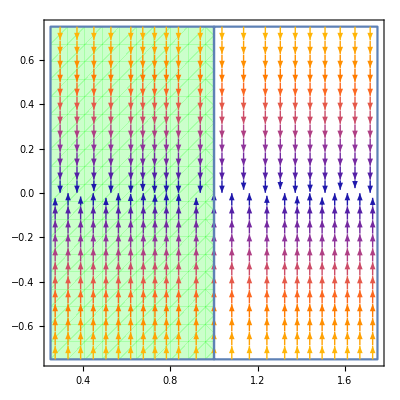

```mathematica
SPL[1,-1,2,0,0,0.75]
```

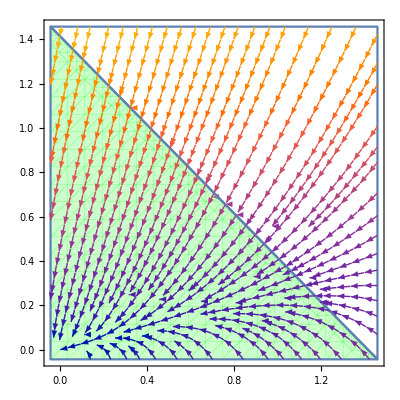

```mathematica
SPL[1,-1,2,0,Pi/4,0.75]
```

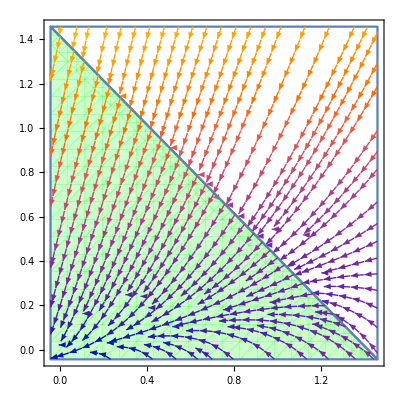

```mathematica
SPL[1,-1,2,0.5,Pi/4,0.75]
```

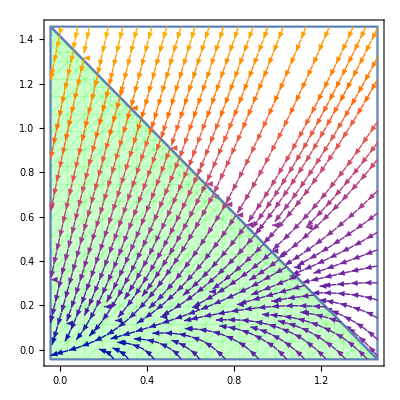

```mathematica
SPL[1,-1,2,0.25,Pi/4,0.75]
```

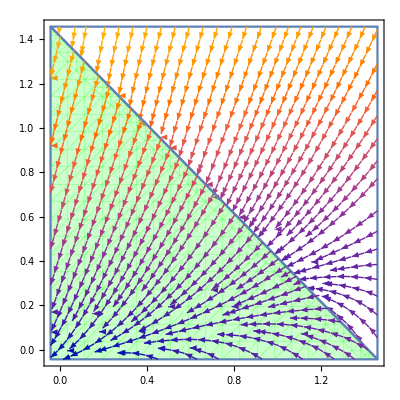

0==(3 exp ℜ (exp ı λ+(3 exp ı p λ)/q) Ω)/(2 R θ)

```mathematica
SPL[1,-1,2,1,Pi/4,0.75]
```

```mathematica
LHS = I κ( (r' + I λ')(1 + E^(-2 I λ)) + I E^(-2 I λ) λ')//FullSimplify
```

κ (ⅈ Cos[λ]+Sin[λ]) (2 Cos[λ] r'+(3 ⅈ Cos[λ]+Sin[λ]) λ')

```mathematica
RHS = E^(3 r) (E^(I λ) + p E^(3I λ))/(2 R)
```

(ⅇ^(3 r) (ⅇ^(ⅈ λ)+ⅇ^(3 ⅈ λ) p))/(2 R)

```mathematica
Eqc =FullSimplify[ComplexExpand[ReIm[LHS == RHS]],{λ,r, λ', r'} ϵ Reals]
```

{2 κ Sin[2 λ] r'==(ⅇ^(3 r) (Cos[λ]+p Cos[3 λ]))/R+2 κ (1+2 Cos[2 λ]) λ',4 κ Cos[λ] (Cos[λ] r'+2 Sin[λ] λ')==(ⅇ^(3 r) (Sin[λ]+p Sin[3 λ]))/R}

```mathematica
EQAll = Append[Eqc,Tan[θ-λ] R'+R ==0]
```

{2 κ Sin[2 λ] r'==(ⅇ^(3 r) (Cos[λ]+p Cos[3 λ]))/R+2 κ (1+2 Cos[2 λ]) λ',4 κ Cos[λ] (Cos[λ] r'+2 Sin[λ] λ')==(ⅇ^(3 r) (Sin[λ]+p Sin[3 λ]))/R,R+Tan[θ-λ] R'==0}

```mathematica
SubAll = # -> #[θ]& /@ { r,λ,r',λ',R,R'}
```

{r→r[θ],λ→λ[θ],r'→r'[θ],λ'→λ'[θ],R→R[θ],R'→R'[θ]}

```mathematica
ClearAll[dsol,p,r,θ];
dsol[p0_,κ0_,λ0_,eps_]:=NDSolve[
Join[EQAll/.SubAll,
{λ[λ0 +eps]==λ0,
r[λ0 +eps]==0,
R[λ0 +eps]==1}]/.{p->p0, κ->κ0},
{λ[θ],r[θ], R[θ]},{θ,λ0 +eps,Pi/2 -eps}]
```

```mathematica
ss=dsol[-0.1,0.1,0,0.001]
```

{{λ[θ]→InterpolatingFunction[…][θ],r[θ]→InterpolatingFunction[…][θ],R[θ]→InterpolatingFunction[…][θ]}}

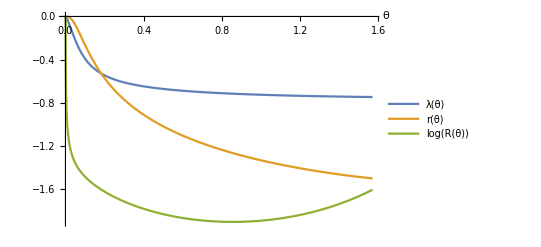

```mathematica
Plot[{λ[θ]/.ss,r[θ]/.ss,Log[R[θ]]/.ss},{θ,0.001,Pi/2-0.001},PlotRange->All,PlotLegends->{λ[θ],r[θ],Log[R[θ]]},AxesLabel->{θ,None}]
```

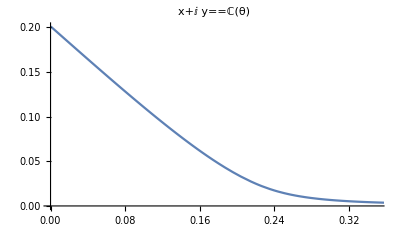

```mathematica
ParametricPlot[With[{r=R[θ]/.ss},{r Cos[θ], r Sin[θ]}],
{θ,0.001,Pi/2-0.001},PlotLabel->x + I y ==ℂ[θ]]
```